# K-mouflage equation checks

This notebook was used to check the consistency of the background equations and nonlinear effective Newton’s constant in the K-mouflage model described in arXiv papers 2110.00566 and 1608.00522.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bbose/Desktop/Code_comparison/Kmouflage

```mathematica
Clear["Global`*"];
```

## A) Check the MG-GLAM background equations [2110.00566]

We check the Friedmann and Klein-Gordan equations found in 2110.00566 which we then have implemented in ReACT. The relevant equations are: Eq.3.54-3.61 of the arXiv version.

## Canonical kinetic term and K-mouflage term, X-derivatives and conformal factor

```mathematica
Xglam[lam_,pd_]:=1/(2 H0^2 lam^2) *  pd^2
Kglam[K0_,lam_,pd_,n_]:=-1+Xglam[lam,pd]+K0 Xglam[lam,pd]^n
KXglam[K0_,lam_,pd_,n_]:=1+K0 n Xglam[lam,pd]^(n-1)
KXXglam[K0_,lam_,pd_,n_]:=K0 n (n-1) Xglam[lam,pd]^(n-2)

Aphiglam[p_,beta_]:=Exp[p*beta]
```

## 1) Check the 1st Friedmann equation (Hubble factor)

### Procedure:

we first solve the Friedmann equations given in Eq. 3.58 and Eq. 3.55 of 2110.00566 for the conformal, normalised Hubble factor squared with n=2 & 3.

we then check consistency between these two equations.

### Notes:

ϕ (=p) is normalised by Planck mass and pd is as in Eq.3.58 and 3.55 of the paper.

Corrected two mistakes in Eq. 3.58 found by using Brax et al. 2014 [1403.5420]:

ϕ^2 in first bracket not ϕ

Missing factor of a^2 in last term

### Friedmann Equations - we express exactly as in the paper so H2 and phi derivatives are different - see 2110.00566 - in the equations.

```mathematica
EQ355[H2_,Om_,n_,lam_,K0_,beta_,pd_,p_,a_]:=H2-Aphiglam[beta,p]*Om  H0^2/a^3-1/3 KXglam[K0,lam,pd,n]*pd^2+1/3 lam^2 H0^2 Kglam[K0,lam,pd,n]
```

```mathematica
EQ358[H2_,Om_,n_,lam_,K0_,beta_,pd_,p_,a_]:= H2(1-1/6 pd^2)- Aphiglam[p,beta] Om /a - 1/3 lam^2 a^2 - (2n-1)/3 * lam^2 a^2 K0 (pd^2/(2 lam^2a^2))^n * H2^n;
```

### Check n=2 case for consistency and solve for analytic solution for conformal Hubble factor to put into ReACT

#### Solve using Eq.3.58 for n=2. Choose root that gives real result.

```mathematica
n2=2;
H2confglamn2A[Om_,lam_,K0_,beta_,pd_,p_,a_]:= Solve[EQ358[H2,Om,n2,lam,K0,beta,pd,p,a]==0,H2][[2,1,2]]
```

```mathematica
funcn2A[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Simplify[H2confglamn2A[Om,lam,K0,beta,pd,p,a]]
```

```mathematica
funcn2A[Om,lam,K0,beta,pd,p,a]
```

-(a^2 lam^2 (-6+pd^2+√(36-12 pd^2+(1-12 K0-(36 ⅇ^(beta p) K0 Om)/(a^3 lam^2)) pd^4)))/(3 K0 pd^4)

#### Solve using Eq.3.55 for n=2. We convert phi derivative and Hubble to conformal Hubble. Choose root that gives real result.

```mathematica
H2confglamn2B[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Solve[EQ355[H2*H0^2/a^2,Om,n2,lam,K0,beta,pd * Sqrt[H2*H0^2/a^2],p,a]==0,H2][[2,1,2]];
```

```mathematica
funcn2B[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Simplify[H2confglamn2B[Om,lam,K0,beta,pd,p,a]]
```

```mathematica
Simplify[funcn2B[Om,lam,K0,beta,pd,p,a]]
```

-(a^2 lam^2 (-6+pd^2+a^2 √(-(36 ⅇ^(beta p) K0 Om pd^4)/(a^7 lam^2)+(36-12 pd^2+pd^4-12 K0 pd^4)/a^4)))/(3 K0 pd^4)

#### Check consistency of solutions to Eq.3.58 and Eq.3.55 for n=2:

```mathematica
Assuming[a>0,Simplify[funcn2A[Om,lam,K0,beta,pd,p,a]-funcn2B[Om,lam,K0,beta,pd,p,a]]]
```

0

### Check n=3 case for consistency and solve for analytic solution for conformal Hubble factor [this has not been implemented in ReACT]

#### Solve using Eq.3.58 for n=3. We need the real root so we check solutions vs n=2 case (they should match at early times).

```mathematica
n3=3;
H2confglamn3A[Om_,lam_,K0_,beta_,pd_,p_,a_]:= Solve[{EQ358[H2,Om,n3,lam,K0,beta,pd,p,a]==0,pd<0},H2][[2,1,2]]
```

```mathematica
funcn3A[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Simplify[H2confglamn3A[Om,lam,K0,beta,pd,p,a]]
```

```mathematica
funcn3A[Om,lam,K0,beta,pd,p,a]
```

$Aborted

#### Solve using Eq.3.55 for n=3. We convert phi derivative and Hubble to conformal Hubble. Choose root that gives real result.

```mathematica
H2confglamn3B[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Solve[{EQ355[H2*H0^2/a^2,Om,n3,lam,K0,beta,pd * Sqrt[H2*H0^2/a^2],p,a]==0},H2][[1,1,2]]
```

```mathematica
H2confglamn3B[Om,lam,K0,beta,pd,p,a]
```

(4 2^(1/3) a^4 lam^4 (-6+pd^2))/(5400 a^6 K0^2 lam^6 pd^12+16200 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12+√(864000 a^12 K0^3 lam^12 pd^18 (-6+pd^2)^3+(5400 a^6 K0^2 lam^6 pd^12+16200 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12)^2))^(1/3)-1/(15 2^(1/3) K0 pd^6)(5400 a^6 K0^2 lam^6 pd^12+16200 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12+√(864000 a^12 K0^3 lam^12 pd^18 (-6+pd^2)^3+(5400 a^6 K0^2 lam^6 pd^12+16200 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12)^2))^(1/3)

```mathematica
funcn3B[Om_,lam_,K0_,beta_,pd_,p_,a_]:=Simplify[H2confglamn3B[Om,lam,K0,beta,pd,p,a]]
```

#### Check consistency of solutions to Eq.3.58 and Eq.3.55 for n=3:

```mathematica
Assuming[a>0,Simplify[funcn3A[Om,lam,K0,beta,pd,p,a]-funcn3B[Om,lam,K0,beta,pd,p,a]]]
```

0

```mathematica
FullSimplify[funcn3A[Om,lam,K0,beta,pd,p,a]]
```

(2 (2/15)^(1/3) a^4 lam^4 (-6+pd^2))/((45 a^6 K0^2 lam^6 pd^12+135 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12+√15 √(a^6 K0^3 lam^8 pd^18 (135 K0 (a^3 lam^2+3 ⅇ^(beta p) Om)^2 pd^6+4 a^6 lam^4 (-6+pd^2)^3)))^(1/3))-((2/15)^(2/3) (45 a^6 K0^2 lam^6 pd^12+135 a^3 ⅇ^(beta p) K0^2 lam^4 Om pd^12+√15 √(a^6 K0^3 lam^8 pd^18 (135 K0 (a^3 lam^2+3 ⅇ^(beta p) Om)^2 pd^6+4 a^6 lam^4 (-6+pd^2)^3)))^(1/3))/(K0 pd^6)

#### Investigate initial value of solution as in code (we require it to be real!):

```mathematica
pi= 10^(-30);
pdi=-10^(-6);
ai=3*10^(-5); 
myOm = 0.3089;
mylam=1.476;
mybeta = 0.2;
myK0 = 1;
funcn3A[myOm,mylam,myK0,mybeta,pdi,pi,ai]
funcn2A[myOm,mylam,myK0,mybeta,pdi,pi,ai]
H2test[myOm,mylam,myK0,mybeta,pdi,pi,ai]
```

10296.7

7.84287×10^15

4.96027×10^9

```mathematica
pdi= -0.1506852;
pi=-0.09381471;
ai=0.09297; 
myOm = 0.3089;
mylam=1.476;
mybeta = 0.2;
myK0 = 1;
H2test[myOm,mylam,myK0,mybeta,pdi,pi,ai]
```

29.3462-49.3838 ⅈ

## 2) Check 2nd Friedmann equation (Hubble derivative) for n=2

### Procedure:

we check consistency between Eq. 3.56 and Eq. 3.59 of 2110.00566 for the Hubble derivative

### Equation 3.59: Conformal time conformal Hubble derivative

#### Typos found in Eq. 3.59 of 2110.00566

1/3 lam^2 a^2 not 2/3

1/3 not 2/3 H^2 pd^2

Missing 1/2 in last term

Basically last 3 terms have a missing 1/2 factor

#### Conformal normalised Hubble derivative: Eq. 3.59 with n=2

```mathematica
Hpconfglam[Om_,lam_,K0_,beta_,pd_,p_,a_]:=-Om/2*Aphiglam[p,beta]/a +1/3*a^2*lam^2 -1/3*H2confglamn2A[Om,lam,K0,beta,pd,p,a]*pd^2 -K0*a^2*lam^2*(H2confglamn2A[Om,lam,K0,beta,pd,p,a]*pd^2/(2*lam^2*a^2))^2
```

```mathematica
Expand[Hpconfglam[Om,lam,K0,beta,pd,p,a]]
```

(2 a^2 lam^2)/3+(a^2 lam^2)/(18 K0)+(ⅇ^(beta p) Om)/(2 a)-(2 a^2 lam^2)/(K0 pd^4)+(2 a^2 lam^2 √(1-pd^2/3+pd^4/36-(K0 pd^4)/3-(ⅇ^(beta p) K0 Om pd^4)/(a^3 lam^2)))/(K0 pd^4)+(a^2 lam^2 √(1-pd^2/3+pd^4/36-(K0 pd^4)/3-(ⅇ^(beta p) K0 Om pd^4)/(a^3 lam^2)))/(3 K0 pd^2)

### Equation 3.56: Cosmic time Hubble derivative

#### Typos found in Eq. 3.56

Last two terms have missing factor of 1/2

#### The Hubble time derivative, not normalised : Eq. 3.56 with n=2

```mathematica
Hpglam[Om_,lam_,K0_,beta_,pd_,p_,n_,a_]:=-Aphiglam[beta,p]*Om H0^2/a^3/2-1/6 KXglam[K0,lam,pd,n]*pd^2-1/3 lam^2 H0^2 Kglam[K0,lam,pd,n]-funcn2B[Om,lam,K0,beta,pd,p,n,a]*H0^2
```

### Check consistency for n=2: H_conf’ = a^2(H^2 + Hdot)

```mathematica
sol1=FullSimplify[ a^2(Hpglam[Om,lam,K0,beta,pd * Sqrt[H2*H0^2/a^2],p,2,a] + H0^2*funcn2B[Om,lam,K0,beta,pd * Sqrt[H2*H0^2/a^2],p,2,a])/H0^2/.H2->H2confglamn2A[Om,lam,K0,beta,pd,p,a]]
```

(9 ⅇ^(beta p) Om+(a^3 lam^2 (-36+pd^4+12 K0 pd^4+6 √(36-12 pd^2+(1-12 K0-(36 ⅇ^(beta p) K0 Om)/(a^3 lam^2)) pd^4)+pd^2 √(36-12 pd^2+(1-12 K0-(36 ⅇ^(beta p) K0 Om)/(a^3 lam^2)) pd^4)))/(K0 pd^4))/(18 a)

```mathematica
sol2=FullSimplify[Hpconfglam[Om,lam,K0,beta,pd,p,a]]
```

(9 ⅇ^(beta p) Om+(a^3 lam^2 (-36+pd^4+12 K0 pd^4+6 √(36-12 pd^2+(1-12 K0-(36 ⅇ^(beta p) K0 Om)/(a^3 lam^2)) pd^4)+pd^2 √(36-12 pd^2+(1-12 K0-(36 ⅇ^(beta p) K0 Om)/(a^3 lam^2)) pd^4)))/(K0 pd^4))/(18 a)

```mathematica
FullSimplify[sol1/sol2]
```

1

## 3) Klein-Gordon equation - Eq.3.61

```mathematica
n2=2;
```

```mathematica
kgeqglam[Om_,lam_,K0_,beta_,pdd_,pd_,p_,a_]:=((KXglam[K0,lam,pd * Sqrt[H2*H0^2/a^2],myn]+2*Xglam[lam,pd * Sqrt[H2*H0^2/a^2]]*KXXglam[K0,lam,pd * Sqrt[H2*H0^2/a^2],myn])*(funcn2A[Om,lam,K0,beta,pd ,p,a] pdd + Hpconfglam[Om,lam,K0,beta,pd ,p,a]*pd)+2(KXglam[K0,lam,pd * Sqrt[H2*H0^2/a^2],myn]-Xglam[lam,pd * Sqrt[H2*H0^2/a^2]]*KXXglam[K0,lam,pd * Sqrt[H2*H0^2/a^2],myn])*funcn2A[Om,lam,K0,beta,pd,p,a]*pd+3 beta * Aphiglam[p,beta]Om / a)/.H2->funcn2A[Om,lam,K0,beta,pd,p,a]
```

#### Solve Klein Gordon equation

```mathematica
amin=3*10^(-5);
lnamin=Log[amin];
myOm=0.3094;
mylam=1.476;
myK0=1;
mybeta=0.2;
```

```mathematica
sol3=NDSolve[{kgeqglam[myOm,mylam,myK0,mybeta,phi''[lna],phi'[lna],phi[lna],Exp[lna]]==0,phi[lnamin]==10^(-20),phi'[lnamin]==-10^(-6)},phi,{lna,lnamin,0},AccuracyGoal->15,PrecisionGoal->15]
```

{{phi→InterpolatingFunction[…]}}

```mathematica
phi[Log[0.95]]/.sol3
```

{-0.0316657}

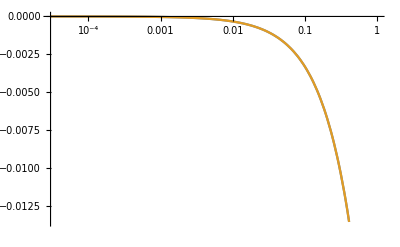

```mathematica
LogLinearPlot[{phi[Log[a]]/.sol3,phi'[Log[a]]/.sol3},{a,amin,1}]
```

## B) Lombriser effective Newton’s constant (Einstein frame) [1608.00522]

We follow Sec. 3.2 of 1608.00522.

### Notes:

1608.00522 uses Einstein frame energy density ρ_E= A ρ. All F_N have an associated conformal factor.

The scalar field is dimensionful.

We  do not assume a sign for K0.

### Derivation of Eq. 3.23 of 1608.00522 - the effective nonlinear Newton’s constant - for any sign of K0 .

#### Eq. 3.22 - the non-canonical kinetic term.

X_lom = (1/ℳ^4) X  where X =1/ 2 (dϕ/dt)^2 and  ℳ^4=(H^2)_0 λ^2 M_pl^2. In ReACT we use d/dlna and the normalised conformal Hubble :  dϕ/dt = H(a) dϕ/dlna  = (ℋ(a)/H_0) (H_0/a) dϕ/dlna .

dX_lom /dX = 1/((H^2)_0 λ^2 M_pl^2) so dK/dX_lom= (dK/dX) (H^2)_0 λ^2 M_pl^2

```mathematica
Klom[X_,K0_,n_]:=-1 + X +K0 X^n 
KX[K0_,X_]:=D[Klom[Xt,K0,2],Xt]/.{Xt->X}
```

#### Solving Klein-Gordon equation for X

Here we define the positive (r-dependent) variable C_A =  54 β^2 G_N^2 M^2 K0 / (8 π G_N ℳ^4) , where y = 1/r^2 and M is the mass enclosed in radius r . Note the - sign on the right hand side does not appear in Winther & Ferreira[1403.6492] (see their eq. 20) - this comes from their definition of X (does not include a - sign).

```mathematica
Assuming[{X∈Reals,CA>0,K0>0},Simplify[Solve[KX[K0,Xl]^2Xl ==-CA y^2/(27 K0) ,Xl]][[1,1,2]]]
```

((-1+(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))^2)/(6 K0 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))

Set this output equal to X. Note this kinetic term is equivalent to -X_Winther[1403.6492] and  ℳ^4X_Brax [1403.5424] where ℳ^4=(H^2)_0 λ^2 M_pl^2.

```mathematica
canX[y_,CA_,K0_,M4_]:=((-(1-(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3)))^2)/(6 K0 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3)) M4
```

#### Solution to the G_eff (Eq.3.23)

Here we define the positive variable  C_B =  3 Sqrt[2] β^2  > 0 and have made a manipulation to rephrase in terms of C_A, C_B and x = -C_A y^2

```mathematica
Gefflom[y_,K0_,CA_,CB_,M4_]:=β/(Mpl GN M )/y  Sqrt[-2 canX[y,CA,K0,M4]] /.{β/(Mpl GN M )-> CB/ Sqrt[CA] * Sqrt[3 K0]/(Sqrt[M4])}
```

```mathematica
FullSimplify[Gefflom[y,K0,CA,CB,M4]^2]
```

-(CB^2 (-1+(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))^2)/(CA y^2 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))

Check expression in paper [Eq. C19]

```mathematica
FullSimplify[Gefflom[y,K0,CA,CB,M4]^2 /.{CA y^2->-x}]/.{CA y^2->-x}
```

-(CB^2 (-1+(1+x+√(x (2+x)))^(1/3))^2)/(CA (1+x+√(x (2+x)))^(1/3) y^2)

Simplified expression:

```mathematica
GefflomB[y_,K0_,CA_,CB_,M4_]:=(CB  Sqrt[(-1+(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))^2])/Sqrt[-CA y^2 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3)]
```

### Check behaviour of solution

#### Check behaviour of the denominator (Cube root factor) for positive and negative K0 (CA)

```mathematica
Denominator[FullSimplify[GefflomB[y,K0,CA,CB,M4]^2*CA*y^2]]
```

(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3)

```mathematica
g[CA_,y_]:=1-CA y^2+√(CA y^2 (-2+CA y^2))
```

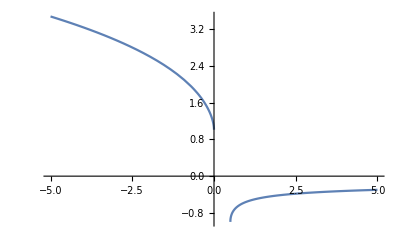

```mathematica
Plot[CubeRoot[g[CA,2]],{CA,-5,5}]
```

#### Check behaviour of the denominator for positive and negative K0 (CA). Select cube root depending on sign of g as shown above

```mathematica
Denominator[FullSimplify[GefflomB[y,K0,CA,CB,M4]]]
```

√(-CA y^2 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))

```mathematica
f[CA_,y_]:=√(-CA y^2 CubeRoot[1-CA y^2+√(CA y^2 (-2+CA y^2))])
```

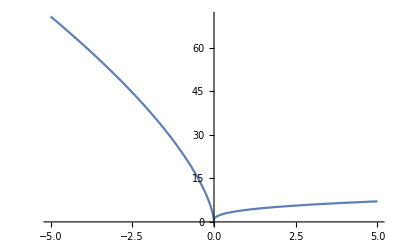

```mathematica
Plot[f[CA,10],{CA,-5,5}]
```

#### Check full expression replacing cube roots with appropriate solution and removing positive factor C_B:

```mathematica
FullSimplify[(GefflomB[y,K0,CA,CB,M4]/CB)]
```

(√((-1+(1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3))^2))/(√(-CA y^2 (1-CA y^2+√(CA y^2 (-2+CA y^2)))^(1/3)))

```mathematica
tot[CA_,y_]:=(√((-1+CubeRoot[1-CA y^2+√(CA y^2 (-2+CA y^2))])^2))/(√(-CA y^2 CubeRoot[1-CA y^2+√(CA y^2 (-2+CA y^2))]))
```

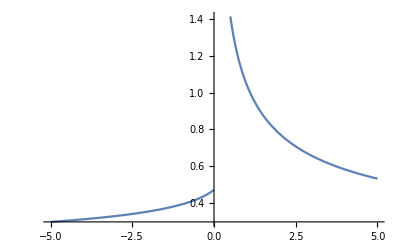

```mathematica
Plot[tot[CA,2],{CA,-5,5}]
```

### Check limits [Eq. 3.25 and Eq.3.26 of 1608.00522]

#### Transform to x assuming K0<0

```mathematica
CB Simplify[tot[CA,y]/.{y^2-> -x^2/CA}]
```

(CB √((-1+(1+x^2+√(x^2 (2+x^2)))^(1/3))^2))/(√(x^2 (1+x^2+√(x^2 (2+x^2)))^(1/3)))

```mathematica
myexp[x_,CB_]:=CB tot[CA,y]/.{y^2-> -x^2/CA}
lucasexp[x_,β_]:=-3 √2 β^2(1-(1+x^2+x √(2+x^2))^(1/3))/(x (1+x^2+x √(2+x^2))^(1/6))
```

#### Large scale limit (r→Infinity;x→ 0 )

```mathematica
Limit[myexp[x,CB],x->0]/.{CB-> 3 Sqrt[2]  β^2}
Limit[lucasexp[x,β],x->0]
```

2 β^2

2 β^2

#### Small scale limit (r→0;x→ Infinity )

```mathematica
LargexRules={a_+x^2->x^2};

simplifiedExpressionA=FullSimplify[myexp[x,CB]/.LargexRules/.{a_+(x^2)^(1/3)->(x^2)^(1/3)}/.{x^2->-CA/r^4}]
```

(CB √(((CA/r^4)^(1/3))^2))/(√((CA (CA/r^4)^(1/3))/r^4))

```mathematica
FullSimplify[simplifiedExpressionA^2]
```

(CB^2 r^4 (CA/r^4)^(1/3))/CA

Check Lucas’ limits

```mathematica
simplifiedExpressionB=FullSimplify[Simplify[lucasexp[x,β]/.LargexRules]/.{-1+(x^2)^(1/3)->(x^2)^(1/3)}]/.{3 √2 β^2->C2}/.{x->C2/r^2 }
```

```mathematica
FullSimplify[simplifiedExpressionB^2/simplifiedExpressionA^2/.{CA->C2^2}]
```

Piecewise[{{1, C2^2/r^2≥0}, {(-1)^(2/3), True}}]

#### Check Eq. 3.26

```mathematica
C2lom = 3 β  Sqrt[8 π GN] M/(2 π ℳ^2) Sqrt[-3 K0];
CAre = -54 β^2 M^2 K0 GN^2/ℳ^4  1/(8 π GN );
```

```mathematica
check=Sqrt[Simplify[C2lom^2/(CAre)]]
```

2 √2

```mathematica
check^2
```

8

```mathematica
CA= C2^2 /2 Sqrt[2]
```

C2^2/(√2)

```mathematica
CA^(-1/3)
```

2^(1/6)/((C2^2)^(1/3))

### PPF Expression:

#### General expressions for PPF G_eff/G_N: Eq. 5.3

```mathematica
y0[p4_,p5_,p6_,p7_]:=p4*a^p5*(2 G H0 M)^p6 (yenv/yh)^p7
PPF[p1_,p2_,p3_,p4_,p5_,p6_,p7_]:=p1*p2*(y/y0[p4,p5,p6,p7])^(p1/(p1-1)p3)*((1+(y/y0[p4,p5,p6,p7])^(p1/(1-p1)p3))^1/p1-1)
```

In general we replace r→a r_th y_h

#### p_2

2. We find from the small x (large r) limit:  p1 * p2 = 2 β^2.

```mathematica
cond2[p2_]:=p2 -2 β^2
```

```mathematica
solp2=Solve[cond2[p2]==0,p2]
```

{{p2→2 β^2}}

#### p_3

1. We find from large x (small r) limit:  p1 p2 (y/y_0)^(p1 p3 /(p1-1)) = (CB (a r_th y)^(4/3))/(-CA)^(1/3) . Comparing powers of y implies p1 p3/(p1-1) = 4/3:

```mathematica
cond1[p1_,p3_]:=p1/(p1-1)p3 - 4/3
```

```mathematica
solp3=Solve[cond1[p1,p3]==0,p3]
```

{{p3→(4 (-1+p1))/(3 p1)}}

#### p_(4-7)

3. We now compare the coefficient of y :  

p1 p2 (1/y_0)^(p1 p3 /(p1-1)) = (CB (a r_th)^(4/3))/(-CA)^(1/3) .

 We can replace:
 
   r_th=[M/(4/3 π ρ a^3(1+δ))]^(1/3) 

with 

ρ=3 Ω_(m,0)H_0^2 /(8π G a^3)  , 
  
  CB = 3 Sqrt[2] β^2 , 
  
  CA = 54 β^2 G^2 M^2 K_0/(H_0^2 λ^2). 
  
  We further approximate (1+δ)=1.

```mathematica
cond3[p1_,p2_,p3_,p4_,p5_,p6_,p7_]:= y0[p4,p5,p6,p7]^(p1 p3/(1-p1))
```

```mathematica
Exp1=Simplify[cond3[p1,p2,p3,p4,p5,p6,p7]/.solp2[[1]]/.solp3[[1]]]
```

1/((2^p6 a^p5 (G H0 M)^p6 p4 (yenv/yh)^p7)^(4/3))

```mathematica
Exp2=Simplify[(CB/CubeRoot[-CA ] * (a rth)^(4/3) )/.{CB->3 Sqrt[2]*β^2,CA-> 54 β^2 G^2 M^2 Subscript[K, 0]/(Subscript[H, 0]^2 λ^2),rth-> (M/(4/3 π ρ a^3 ))^(1/3)}/.{ρ-> 3 Subscript[Ω, m0] Subscript[H, 0]^2/(8 G π a^3)}]
```

-(2^(11/18) β^2 (a ((G M)/(H_0^2 Ω_m0))^(1/3))^(4/3))/(((G^2 M^2 β^2 K_0)/(λ^2 H_0^2))^(1/3))

#### p_5

Compare power of a

```mathematica
-(2^(11/18) β^2 (a ((G M)/(Subscript[H, 0]^2 Subscript[Ω, m0]))^(1/3))^(4/3))/(((G^2 M^2 β^2 Subscript[K, 0])/(λ^2 Subscript[H, 0]^2))^(1/3))
```

```mathematica
solp5=Solve[-(4/3*p5)==(4/3),p5]
```

{{p5→-1}}

#### p_7

Compare power of yenv/yh

```mathematica
p7 = 0;
```

#### p_6

Compare power of  (G M)

```mathematica
Numerator[-(2^(11/18) β^2 (a ((G M)/(Subscript[H, 0]^2 Subscript[Ω, m0]))^(1/3))^(4/3))/(((G^2 M^2 β^2 Subscript[K, 0])/(λ^2 Subscript[H, 0]^2))^(1/3))]
Denominator[-(2^(11/18) β^2 (a ((G M)/(Subscript[H, 0]^2 Subscript[Ω, m0]))^(1/3))^(4/3))/(((G^2 M^2 β^2 Subscript[K, 0])/(λ^2 Subscript[H, 0]^2))^(1/3))]
```

-2^(11/18) β^2 (a ((G M)/(H_0^2 Ω_m0))^(1/3))^(4/3)

((G^2 M^2 β^2 K_0)/(λ^2 H_0^2))^(1/3)

```mathematica
solp6=Solve[-(4/3*p6)==(4/9-2/3),p6]
```

{{p6→1/6}}

#### p_4 - the remaining coefficient

Remove all accounted for terms

```mathematica
Exp3=Simplify[cond3[p1,p2,p3,p4,p5,p6,0]/.solp2[[1]]/.solp3[[1]]]/.solp5[[1]]/.solp6[[1]]
```

1/(2^(2/9) (((G H0 M)^(1/6) p4)/a)^(4/3))

```mathematica
Solve[p1 p2 Exp3==Exp2,p4]
```

{{p4→-((-1)^(1/4) √G √H0 √M p1^(3/4) p2^(3/4) √H_0 K_0^(1/4) ((G M)/(H_0^2 Ω_m0))^(1/6) √Ω_m0)/(2^(5/8) (G H0 M)^(2/3) β √λ)},{p4→((-1)^(1/4) √G √H0 √M p1^(3/4) p2^(3/4) √H_0 K_0^(1/4) ((G M)/(H_0^2 Ω_m0))^(1/6) √Ω_m0)/(2^(5/8) (G H0 M)^(2/3) β √λ)},{p4→-((-1)^(3/4) √G √H0 √M p1^(3/4) p2^(3/4) √H_0 K_0^(1/4) ((G M)/(H_0^2 Ω_m0))^(1/6) √Ω_m0)/(2^(5/8) (G H0 M)^(2/3) β √λ)},{p4→((-1)^(3/4) √G √H0 √M p1^(3/4) p2^(3/4) √H_0 K_0^(1/4) ((G M)/(H_0^2 Ω_m0))^(1/6) √Ω_m0)/(2^(5/8) (G H0 M)^(2/3) β √λ)}}

```mathematica
FullSimplify[-(√G √H0 √M p1^(3/4) p2^(3/4) √Subscript[H, 0] Subscript[K, 0]^(1/4) ((G M)/(Subscript[H, 0]^2 Subscript[Ω, m0]))^(1/6) √Subscript[Ω, m0])/(2^(5/8) (G H0 M)^(2/3) β √λ)/.{ G H0 M -> 1/2}/.{√G √H0 √M ->1/√2}/.{G M -> 1/(2 Subscript[H, 0])}/.solp2[[1]] ]
```

-(2^(1/8) p1^(3/4) (β^2)^(3/4) √H_0 K_0^(1/4) (1/(H_0^3 Ω_m0))^(1/6) √Ω_m0)/(β √λ)

```mathematica
-(2^(1/8) p1^(3/4) (β^2)^(3/4)  Subscript[K, 0]^(1/4))/(β √λ)Subscript[Ω, m0]^(1/3) = (-(2^(1/2) p1^3 β^2  Subscript[K, 0])/λ^2)^(1/4)Subscript[Ω, m0]^(1/3)
```